## Modelo de Ising 2D - Algoritmo de Metropolis

Para realizar as simulações do modelo de Ising em 2 dimensões, primeiro definimos as funções que serão utilizadas e uma breve descrição de sua finalidade.

x[] garante que as condições de contorno sejam satisfeitas

```mathematica
x[coor_]:=If[coor == 0,size,
                           If[coor == size+1,1,
                                        coor]]
```

flipEnergy gera aleatoriamente um dos spins da matriz e chama a função DeltaEnergy

```mathematica
flipEnergy:=Module[{i,j},
i=Random[Integer,{1,size}];
j=Random[Integer,{1,size}];
DeltaEnergy[i,j]; 
];
```

DeltaEnergy faz a soma dos quatro vizinhos em torno do spin sorteado e calcula a diferença de energia. Se a energia U ≤ 0, substitui o spin. Caso contrário, chama a função MonteCarlo

```mathematica
DeltaEnergy[i_,j_]:= Module[{sum, energy},
          sum = ising[[x[i-1],j]]+ ising[[x[i+1],j]]+
          ising[[i,x[j-1]]]+ising[[i,x[j+1]]] ; (* sum of 4 neighbours*)
	energy =2(J )( sum)(ising[[i,j]]);
          If[ energy<=0,ising[[i,j]]=-ising[[i,j]],Montecarlo[i,j,energy]]
]
```

MonteCarlo gera um numero aleatorio r entre 0 e 1. Caso r≤ⅇ^(-U/T), substitui o spin. Caso contrário, deixa inalterado.

```mathematica
Montecarlo[i_,j_,U_]:=
                           If[Random[]<ⅇ^(- U/(T)),ising[[i,j]]=-ising[[i,j]]]
```

GenerateMatrix[op] gera a matriz de spins.
Se o parametro for -1 → gera matriz totalmente negativa (spins pra baixo)
Se o parametro for 1 → gera matriz totalmente positiva (spins pra cima)
Se o parametro for 0 → gera matriz totalmente aleatoria (probabilidade de spin negativo = probabilidade de spin positivo)
Se o parametro for outro numero N inteiro positivo (2, 3, 4, 5...) -> gera matriz majoritariamente positiva na relação N/1

```mathematica
GenerateMatrix[op_] := Module[{i,j,mat},
If[op==-1, Return [Table[-1,{i,1,size},{j,1,size}]], (*entirely negative matrix *) 
If [op == 1, Return [Table[1,{i,1,size},{j,1,size}]],  (*entirely positive matrix *)
If [op==0, Return [Table[2Random[Integer]-1,{i,1,size},{j,1,size}]]  , (*entirely random matrix *)
mat =  Table[0,{i,1,size},{j,1,size}];
For[i=1,i≤size,i++,
	For[j=1,j≤size,j++,
		If[RandomInteger[op]==0, mat[[i]][[j]]=-1, mat[[i]][[j]]=1] (*mostly positive matrix *)
	
]
];
Return[mat]
]]]]
```

```mathematica
GetHighestTemp[list_] := Flatten[#[[First@Position[#,Max@#]&@(Last/@#)]]&@list]
```

FitPolynomial pega uma lista de valores e gera um ajuste polinomial de grau 10.

```mathematica
FitPolynomial[data_,potencia_]:=Fit[data,Table[x^n,{n,0,potencia}],x]
```

Define configurações para o notebook.

```mathematica
SetOptions[ArrayPlot, Mesh -> False,PlotRange->{-1,1}];
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"];
```

Uma vez definidas as funções gerais, começamos os casos de simulação. 
Neste primeiro caso, escolhemos uma temperatura fixa T=2 (em unidades naturais), geramos uma lista de valores para J = {-4, -3, -2, -1, 0, 1, 2, 3, 4}, configuramos a quantidade de passos na animação e o tamanho da matriz de spins

```mathematica
Jlist = Range[-4,4,1];
steps = 500;
T = 2;
size=100;
```

Dada as configurações iniciais, partimos para a primeira simulação, onde podemos ver o comportamento dos spins ao longo das interações.

```mathematica
For[i=1,i<=Dimensions[Jlist][[1]],i++,
 count =0; J = Jlist[[i]];
ising = GenerateMatrix[0];
isingInit = ising;

Print["J=", Jlist[[i]], ListAnimate[Flatten[{{ArrayPlot[isingInit]},Table[
	Do[flipEnergy,50];
          ArrayPlot[ising],
                 steps]}]]];
 
]
```

J=-4

J=-3

J=-2

J=3

J=4

Nos graficos animados, os pontos brancos representam spin -1 e os pontos escuros representam spin +1. É possível notar que para valores de J < 0, não há um comportamento magnetico, como esperado. De modo geral, a magnetização não se altera. Já para valores de J > 0, há uma tendência de aglomeração dos spins na matriz.
Agora simularemos a magnetização e susceptibilidade em função da temperatura para diferentes valores de J. Iniciamos com as configurações gerais

```mathematica
Tlist = Range[0.1,8,0.1]; (* list of temperatures *)
Jlist = Range[-2,2,0.5]; (* lis to J values*) 
magnetizationList = {}; (* initialization values*) 
magJ = {};
magJ1 = {};
susceptibilityList = {};
susJ = {};
susJ1 = {};

steps = 50000; (* repetitions of metropolis algorithm *)
size=40;
```

Agora faremos a simulação. Como a constante de Boltzmann é escolhida como 1, as temperaturas apresentadas são medidas em multiplos da constante de Boltzmann ao invés do valor esperado em K.

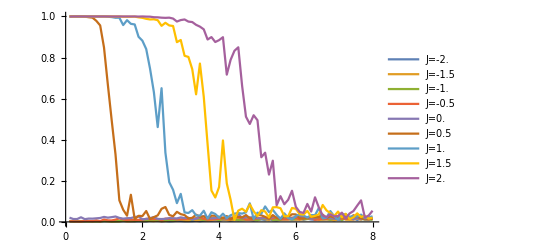

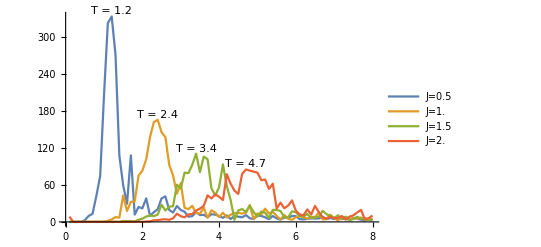

```mathematica
For[j=1,j<=Dimensions[Jlist][[1]],j++,
	J = Jlist[[j]];
	For[i=1,i<=Dimensions[Tlist][[1]],i++, (* execute process over different temperature values*)
	count =0;magnetizationGraph = {}; susceptibilityGraph = {};(*reset control variables *)
	T = Tlist[[i]]; (*set new temperature  *)
	
	ising=GenerateMatrix[3];
	isingInit = ising;
	Do[AppendTo[magnetizationGraph ,{++count,Abs[Total[Total[ising]]]/size^2}];
	     AppendTo[susceptibilityGraph ,{++count,(Abs[Total[Total[ising]]]/size^2)^2}];		
               flipEnergy,steps]; (* execute metropolis algorithm 'steps' times *)
	AppendTo[magnetizationList,{Tlist[[i]], Mean[magnetizationGraph[[-Dimensions[magnetizationGraph][[1]]/10;;]] ][[2]]}];
If[Jlist[[j]]>0,
AppendTo[susceptibilityList, {Tlist[[i]], size^2/Tlist[[i]](Mean[magnetizationGraph[[-Dimensions[susceptibilityGraph][[1]]/10;;]] ][[2]]  -(Mean[magnetizationGraph[[-Dimensions[magnetizationGraph][[1]]/10;;]] ][[2]])^2 )}]
]];
AppendTo[magJ, magnetizationList];
magnetizationList = {};
AppendTo[magJ1, Jlist[[j]]];
If[Jlist[[j]]>0,
AppendTo[susJ,susceptibilityList];
susceptibilityList = {};
AppendTo[susJ1,Jlist[[j]]];]

]
ListPlot[magJ, Joined->True, PlotLegends->Flatten[Table[{"J="<>ToString[magJ1[[i]]]},{i,Dimensions[magJ1][[1]]}]], AxesLabel->{"Temperatura", "Magnetização"}    ] 
Show[ListPlot[susJ, Joined->True, PlotLegends->Flatten[Table[{"J="<>ToString[susJ1[[i]]]},{i,Dimensions[susJ1][[1]]}]], PlotRange->All, AxesLabel->{"Temperatura","Susceptibilidade"}] ,Table[  Graphics[Text["T = "<>ToString[GetHighestTemp[susJ[[i]]][[1]]],GetHighestTemp[susJ[[i]]],{0,-1}]]   ,{i,Dimensions[susJ1][[1]]}] ]
```

Para os calculos acima, realizamos ‘size’ (padrão size = 50000) repetições do algoritmo de metropolis para cada temperatura e cada J, e é considerado apenas as ultimas 5000 iterações, assumindo que neste ponto o sistema ja esteja em equilíbrio. Para os casos onde J é positivo, também é traçada a curva de susceptibilidade por temperatura afim de encontrar as temperaturas críticas. Essas podem ser identificadas pelos picos no gráfico. Para fim de comparação, a solução de Onsager chega a uma temperatura crítica k T_c= (2J)/(Ln(1+√2))≃2.27J. Neste caso, estamos utilizando o valor da constante de Boltzmann k=1, o que resulta numa temperatura crítica T_c= 2.27J, o que deixa os resultados bem próximo do esperado.

Agora, com a intenção de encontrar a lei de escala, vamos recalcular a susceptibilidade para valores diferentes do tamanho da rede. Começamos definindo as condições gerais.

```mathematica
Tlist = Range[0.1,5,0.1]; (* list of temperatures *)
J=1; (* lis to J values*) 
magnetizationList = {}; (* initialization values*) 
magL = {};
magL1 = {};
susceptibilityList = {};
susL = {};
susL1 = {};

steps = 50000; (* repetitions of metropolis algorithm *)
listSize={10, 16, 24, 36};
```

Agora fazendo as simulações

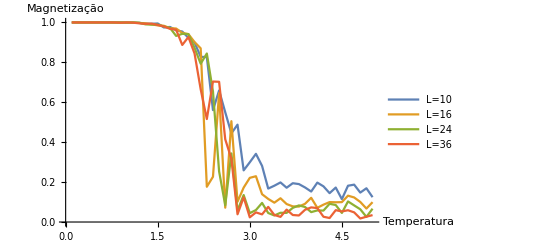

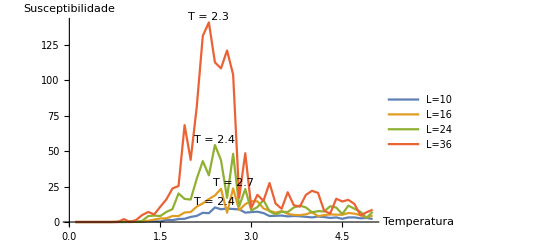

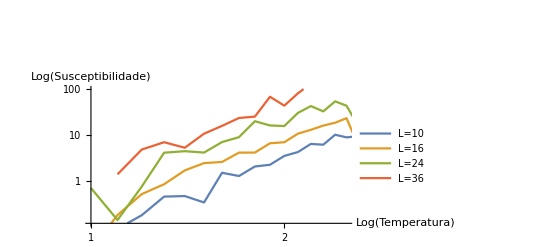

```mathematica
For[j=1,j<=Dimensions[listSize][[1]],j++,
	size = listSize[[j]];
	For[i=1,i<=Dimensions[Tlist][[1]],i++, (* execute process over different temperature values*)
	count =0;magnetizationGraph = {}; susceptibilityGraph = {};(*reset control variables *)
	T = Tlist[[i]]; (*set new temperature  *)
	
	ising=GenerateMatrix[3];
	isingInit = ising;
	Do[AppendTo[magnetizationGraph ,{++count,Abs[Total[Total[ising]]]/size^2}];
	     AppendTo[susceptibilityGraph ,{++count,(Abs[Total[Total[ising]]]/size^2)^2}];		
               flipEnergy,steps]; (* execute metropolis algorithm 'steps' times *)
	AppendTo[magnetizationList,{Tlist[[i]], Mean[magnetizationGraph[[-Dimensions[magnetizationGraph][[1]]/10;;]] ][[2]]}];
AppendTo[susceptibilityList, {Tlist[[i]], size^2/Tlist[[i]](Mean[magnetizationGraph[[-Dimensions[susceptibilityGraph][[1]]/10;;]] ][[2]]  -(Mean[magnetizationGraph[[-Dimensions[magnetizationGraph][[1]]/10;;]] ][[2]])^2 )}]];
AppendTo[magL, magnetizationList];
magnetizationList = {};
AppendTo[magL1, listSize[[j]]];

AppendTo[susL,susceptibilityList];
susceptibilityList = {};
AppendTo[susL1,listSize[[j]]];

]
ListPlot[magL, Joined->True, PlotLegends->Flatten[Table[{"L="<>ToString[magL1[[i]]]},{i,Dimensions[magL1][[1]]}]], AxesLabel->{"Temperatura","Magnetização"}   ] 
Show[ListPlot[susL, Joined->True, PlotLegends->Flatten[Table[{"L="<>ToString[susL1[[i]]]},{i,Dimensions[susL1][[1]]}]], PlotRange->All, AxesLabel->{"Temperatura","Susceptibilidade"}] ,Table[  Graphics[Text["T = "<>ToString[GetHighestTemp[susL[[i]]][[1]]],GetHighestTemp[susL[[i]]],{0,-1}]]   ,{i,Dimensions[susL1][[1]]}] ]
Show[ListLogLogPlot[susL, Joined->True, PlotLegends->Flatten[Table[{"L="<>ToString[susL1[[i]]]},{i,Dimensions[susL1][[1]]}]], PlotRange->{{1,2.5},{0,100}}, AxesLabel->{"Log(Temperatura)","Log(Susceptibilidade)"}] ,Table[  Graphics[Text["T = "<>ToString[GetHighestTemp[susL[[i]]][[1]]],GetHighestTemp[susL[[i]]],{0,-1}]]   ,{i,Dimensions[susL1][[1]]}] ]
```

O primeiro gráfico mostra a magnetização em função da temperatura para diferentes valores do tamanho da rede. É possível notar que o tamanho da rede influencia pouco no comportamento da temperatura. 
O segundo gráfico mostra a susceptibilidade em função da temperatura. É possível notar que a temperatura crítica é semelhante para os vários valores do tamanho da rede, entretanto, o valor máximo da susceptbilidade aumenta de acordo com o tamanho da rede.
Com o intuito de ver a lei de escala, podemos observar o terceiro gráfico que mostra a escala log-log de susceptibilidade por temperatura, onde vemos que se aproximam de retas até a temperatura crítica.